# Optical fourier transforms through a lens

### constants and units

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
mass = 1.44*10^-25;
```

```mathematica
1000/22//N
```

45.4545

```mathematica
45*322
```

14490

```mathematica
0.7(.61)/(.67)*461//N
```

293.801

```mathematica
(.61)/(.67)*461/406.5
```

1.03251

```mathematica
(.61)/(.68)780
```

699.706

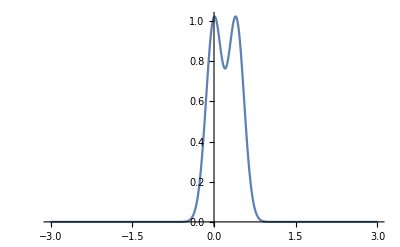

```mathematica
Plot[Exp[(-2*x^2)/(.293)^2]+Exp[(-2*(x-.4065)^2)/(.293)^2],{x,-3,3}, PlotRange-> All]
```

```mathematica
simData = Table[{x,Exp[(-2*x^2)/(.293)^2]+Exp[(-2*(x-.4065)^2)/(.293)^2]},{x,-3,3,16/130}];
```

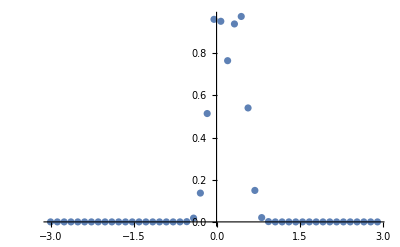

```mathematica
ListPlot[simData,PlotRange-> All]
```

## Computing fourier integrals over apertures

```mathematica
kvec[x_,y_,kl_,f_] = {x,y}*kl/Norm[{x,y,f}];
```

```mathematica
imagePlane[xp_,yp_,waistFP_,f_,kl_,NA_]:= NIntegrate[Exp[(-(x^2+y^2))/waistFP^2]Exp[-I*{xp,yp}.kvec[x,y,kl,f]],{x,-Tan[ArcSin[NA]]*f,Tan[ArcSin[NA]]*f},{y,-Tan[ArcSin[NA]]*f,Tan[ArcSin[NA]]*f}](*in x y integrals*)
```

```mathematica
imagePlane[xp_,yp_,waistFP_,f_,kl_,NA_,diameter_]:= NIntegrate[Exp[(-((f*Sin[θ]Cos[ϕ])^2+(f*Sin[θ]Sin[ϕ])^2))/waistFP^2]Exp[-I*{xp,yp}.kvec[f*Sin[θ]Cos[ϕ],f*Sin[θ]Sin[ϕ],kl,f]]Sin[θ],{θ,ArcTan[diameter/(2*f)],ArcSin[NA]},{ϕ,0,2π}](*in theta phi*)
```

```mathematica
imagePlaneTheta[xp_,yp_,waistFP_,f_,kl_,NA_,diameter_]:= NIntegrate[Exp[(-((f*Sin[θ]Cos[ϕ])^2+(f*Sin[θ]Sin[ϕ])^2))/waistFP^2]Exp[-I*{xp,yp}.kvec[f*Sin[θ]Cos[ϕ],f*Sin[θ]Sin[ϕ],kl,f]]Sin[θ],{θ,0,ArcSin[NA]},{ϕ,0,2π}](*in theta phi*)
```

```mathematica
imagePlaneTheta2[xp_,yp_,waistFP_,f_,kl_,NA_,diameter_]:= NIntegrate[Exp[(-((f*Sin[θ]Cos[ϕ])^2+(f*Sin[θ]Sin[ϕ])^2))/waistFP^2]Exp[-I*{xp,yp}.kvec[f*Sin[θ]Cos[ϕ],f*Sin[θ]Sin[ϕ],kl,f]]Sin[θ],{θ,0,ArcSin[NA]},{ϕ,0,2π}](*in theta phi*)
```

```mathematica
ArcTan[(.01)/(2*.027)]
```

0.183111

```mathematica
ArcTan[(.004)/(2*.0146)]
```

0.136139

```mathematica
Sin[10*π/180]*.005
```

0.000868241

```mathematica
18/5 7//N
```

25.2

```mathematica
10Log[10,.025/1.23]
```

-16.9197

```mathematica
18/5 7*.8*.75*.75
```

11.34

```mathematica
IP1D[x_,waistFP_,f_,kl_,NA_]:= NIntegrate[Exp[(-(f*Tan[θ])^2)/waistFP^2]Exp[-I*kl*Sin[θ]*x],{θ,- ArcSin[NA], ArcSin[NA] }](*1D*)
```

```mathematica
(1.1mm)/(22mm)//N
```

0.05

```mathematica
0.05
```

0.05

```mathematica
ListPlot[IPData1D, PlotRange->All]
```

Interrupted

#### 2D fourier transform: probably some artificating because i’m integrating over a square instead of a circle, should fix, but mostly this works. Amazing how little you have to deviate in NA to get big differences from gaussian optics, and this calculation sin’t even include polarization effects (i.e. assumes full interference although in truth contrast goes down due to tilting of polarization vector).

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlane[x,y,27mm,22mm,(2π)/(461nm),0.68,10mm]]^2},{x,-1μm,1μm,0.1μm},{y,-1μm,1μm,0.1μm}],1];
```

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,100mm,22mm,(2π)/(461nm),0.68,10mm]]^2},{x,-1μm,1μm,0.1μm},{y,-1μm,1μm,0.1μm}],1];
```

#### 2D integral for the imaging system been testing 12/08

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,9.4mm,1740mm,(2π)/(515nm),.0077,10mm]]^2},{x,-40μm,40μm,4μm},{y,-40μm,40μm,4μm}],1];
```

```mathematica
13.5/1000
```

0.0135

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,100mm,1000mm,(2π)/(461nm),.0135,10mm]]^2},{x,-80μm,80μm,4μm},{y,-80μm,80μm,4μm}],1];
```

```mathematica
interpolatedData  = Interpolation[IPData];
```

```mathematica
simData = Table[interpolatedData[x*μm,y*μm]*4.65μm,{x,-25,25},{y,-25,25}];
```

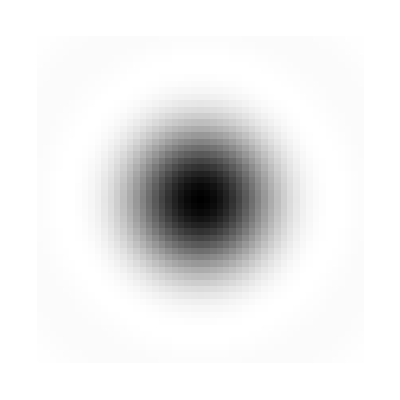

```mathematica
ArrayPlot[simData]
```

```mathematica
dat=Map[Total,simData]
```

{9.38408×10^-13,9.19943×10^-13,8.09231×10^-13,6.99428×10^-13,6.17183×10^-13,5.89143×10^-13,6.16075×10^-13,7.60861×10^-13,1.0605×10^-12,1.55199×10^-12,2.35765×10^-12,3.39503×10^-12,4.66701×10^-12,6.17645×10^-12,8.07387×10^-12,1.01555×10^-11,1.2365×10^-11,1.46464×10^-11,1.70073×10^-11,1.9302×10^-11,2.14489×10^-11,2.33661×10^-11,2.4865×10^-11,2.60136×10^-11,2.67728×10^-11,2.71038×10^-11,2.67728×10^-11,2.60136×10^-11,2.4865×10^-11,2.33661×10^-11,2.14489×10^-11,1.9302×10^-11,1.70073×10^-11,1.46464×10^-11,1.2365×10^-11,1.01555×10^-11,8.07387×10^-12,6.17645×10^-12,4.66701×10^-12,3.39503×10^-12,2.35765×10^-12,1.55199×10^-12,1.0605×10^-12,7.60861×10^-13,6.16075×10^-13,5.89143×10^-13,6.17183×10^-13,6.99428×10^-13,8.09231×10^-13,9.19943×10^-13,9.38408×10^-13}

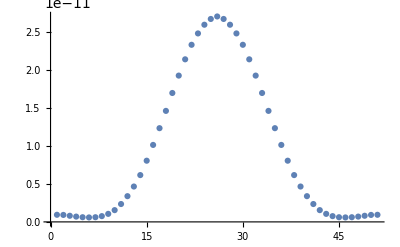

```mathematica
ListPlot[dat]
```

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,1.7mm,30mm,(2π)/(515nm),.2,10mm]]^2},{x,-5μm,5μm,1μm},{y,-5μm,5μm,1μm}],1];
```

```mathematica
fit = NonlinearModelFit[IPData,A Exp[-2(x^2+y^2)/waistFit^2],{{A,1},{waistFit,35μm}},{x,y}];
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.000102176 | 1.05783×10^-8 | 9659.04 | 1.41618583237709×10^-352
waistFit | 2.89523×10^-6 | 2.11951×10^-10 | 13659.9 | 1.7380047132829×10^-370

```mathematica
(*IPData = Flatten[Table[{x,y,photonDistribution[x,y]},{x,-1μm,1μm,0.1μm},{y,-1μm,1μm,0.15μm}],1];*)
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 6.50639×10^-9 | 1.11582×10^-11 | 583.105 | 2.06999493114×10^-636
waistFit | 0.0000346192 | 4.26468×10^-8 | 811.767 | 1.98472990706×10^-699

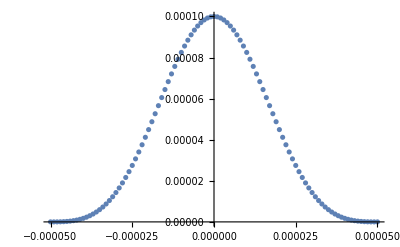

```mathematica
ListPlot[IPData1D]
```

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,10.6mm,1740mm,(2π)/(515nm),0.077]]^2},{x,-50μm,50μm,1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.000116587 | 8.14218×10^-11 | 1.43188×10^6 | 1.78682113159403×10^-512
waistFit | 0.0000269101 | 2.17012×10^-11 | 1.24003×10^6 | 2.73692329584288×10^-506

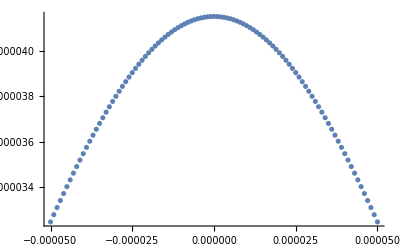

```mathematica
ListPlot[IPData1D]
```

```mathematica
waistFit*(1+(z/(π*waistFit^2/(515nm)))^2)^(1/2)/.{z-> 18mm,waistFit-> 1.75μm}//
N
IPData1D = Table[{x,Norm[IP1D[x,1.7mm,18mm,(2π)/(515nm),0.25]]^2},{x,-10μm,10μm,0.1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
waistFit*(1+(z/(π*waistFit^2/(515nm)))^2)^(1/2)/.{z-> 18mm,fit1D["BestFitParameters"][[2]]}//N
```

0.00168613

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0277963 | 3.48942×10^-6 | 7965.89 | 1.38713232352842×10^-549
waistFit | 1.74938×10^-6 | 2.53582×10^-10 | 6898.66 | 3.74521916659374×10^-537

0.00168673

```mathematica
Sin[ArcTan[1.7/18]]
```

0.094026

```mathematica
1.75-1.68
```

0.07

```mathematica
(*IPDataWAperture = IPData;*)
```

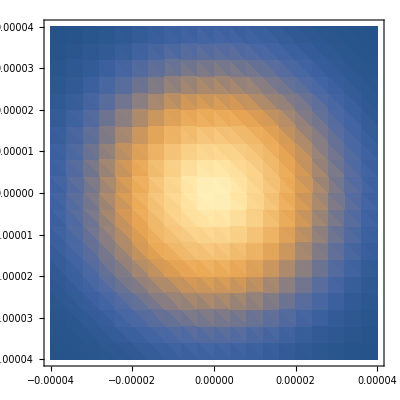

```mathematica
ListDensityPlot[IPData, PlotRange-> All]
```

```mathematica
crossSectionNoAp = Interpolation[IPData];
```

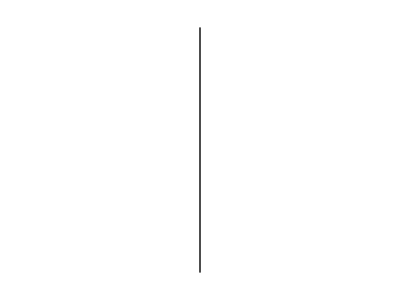

```mathematica
vertLine = Graphics[Line[{{(.61)/(.68)*461nm,0},{(.61)/(.68)*461nm,2}}]]
```

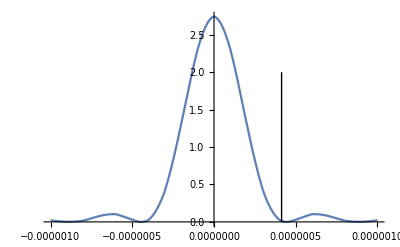

```mathematica
Show[{Plot[crossSectionNoAp[x,0],{x,-1μm,1μm}],vertLine = Graphics[Line[{{(.61)/(.68)*461nm,0},{(.61)/(.68)*461nm,2}}]]}]
```

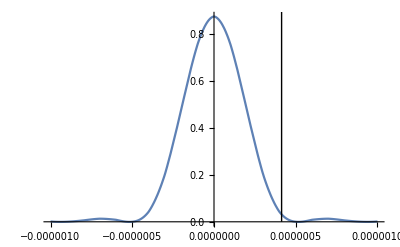

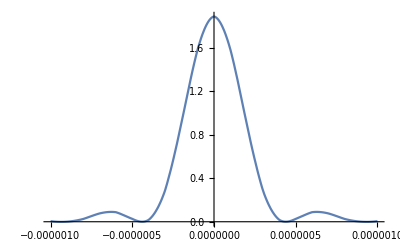

```mathematica
Plot[crossSection[x,0],{x,-1μm,1μm}]
```

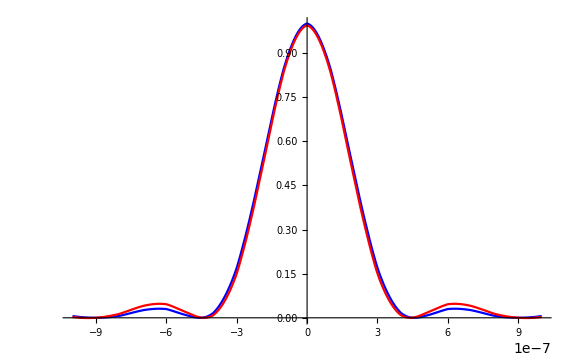

```mathematica
Plot[{crossSectionNoAp[x,0]/2.05,crossSectionWithAp[x,0]/1.9},{x,-1μm,1μm}, PlotStyle-> {Blue, Red}]
```

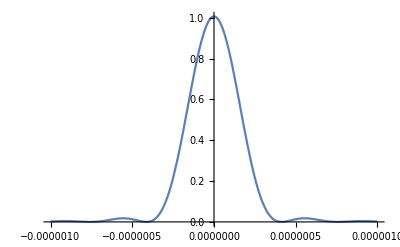

```mathematica
Plot[photonDistribution[x,0]/(6.8*10^12),{x,-1μm,1μm} ]
```

```mathematica
FindMaximum[crossSectionNoAp[x,0]/2.05,{x,450nm}]
```

InterpolatingFunction::dmval: Input value {0.5, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.58899,{x→4.47793×10^-6}}

```mathematica
crossSectionNoAp[590nm,0]/2.05
```

0.027554

```mathematica
crossSectionWithAp[599nm,0]/2.05
```

0.0425621

```mathematica
FindMaximum[photonDistribution[x,0]/(6.8*10^12),{x,600nm}]
```

{0.0176085,{x→5.54229×10^-7}}

```mathematica
NIntegrate[crossSectionWithAp[x,0],{x,-1μm,1μm}]
```

7.8999×10^-7

```mathematica
NIntegrate[crossSectionNoAp[x,0],{x,-1μm,1μm}]
```

8.59244×10^-7

```mathematica
1-(4/14.6)^2
```

0.924939

```mathematica
7.89/8.59
```

0.91851

```mathematica
crossList[[1]][.1μm]
```

-6       -6          -6       -6
InterpolatingFunction[{{-1. 10  , 1. 10  }, {-1. 10  , 1. 10  }}, <>][1.×10^-7]

```mathematica
Plot[crossList[[1]]/.x0-> x,{x,-1μm,1μm}]
```

-Graphics-

```mathematica
(.61)/(.68)*461
```

413.544

```mathematica
vertLine = Graphics[Line[{{(.61)/(.68)*461nm,0},{(.61)/(.68)*461nm,2}}]]
```

-Graphics-

```mathematica
FindRoot[crossSection[x,0],{x,413nm}]
```

{x→4.39208×10^-7}

```mathematica
439/413//N
```

1.06295

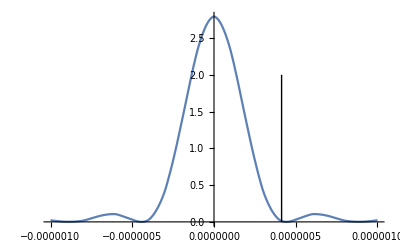

```mathematica
Show[{Plot[crossSection[x,0],{x,-1μm,1μm}],vertLine}]
```

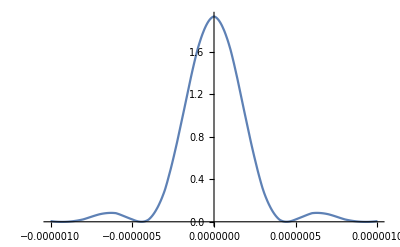

```mathematica
IPDataFull = IPData;
```

```mathematica
IPData2mm= IPData;
```

```mathematica
IPData5mm= IPData;
```

```mathematica
IPData10mm= IPData;
```

```mathematica
Export["/Users/AMK/Dropbox/Lab/JILA/Strontium_neutral/Equipment/Objective_design/apertureData_27mmWaist_0_2mm_5mm_10mm.tsv",{IPDataFull,IPData2mm,IPData5mm,IPData10mm}]
```

/Users/AMK/Dropbox/Lab/JILA/Strontium_neutral/Equipment/Objective_design/apertureData_27mmWaist_0_2mm_5mm_10mm.tsv

```mathematica
crossList = {};
```

```mathematica
AppendTo[crossList,crossSection]
```

{                              -6       -6          -6       -6
InterpolatingFunction[{{-1. 10  , 1. 10  }, {-1. 10  , 1. 10  }}, <>],                              -6       -6          -6       -6
InterpolatingFunction[{{-1. 10  , 1. 10  }, {-1. 10  , 1. 10  }}, <>],                              -6       -6          -6       -6
InterpolatingFunction[{{-1. 10  , 1. 10  }, {-1. 10  , 1. 10  }}, <>],                              -6       -6          -6       -6
InterpolatingFunction[{{-1. 10  , 1. 10  }, {-1. 10  , 1. 10  }}, <>]}

```mathematica
leg = SwatchLegend[{Black,Red,Green, Blue},{"0 mm","2mm","5mm","10mm"}];
```

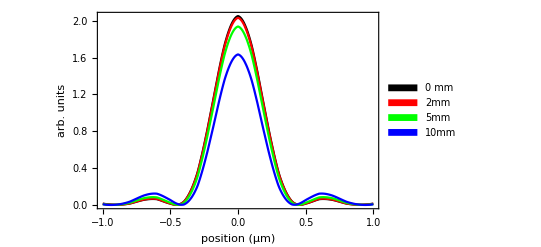

```mathematica
Legended[Show[MapThread[Plot[#1[x*μm,0],{x,-1,1}, PlotRange-> All, PlotStyle->#2]&,{crossList,{Black,Red,Green, Blue}}], Frame-> True, Axes-> False, FrameLabel-> {"position (μm)","arb. units"}],leg]
```

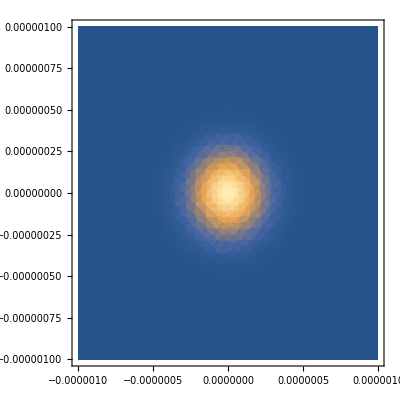

```mathematica
DensityPlot[fit[x,y],{x,-1μm,1μm},{y,-1μm,1μm}, PlotRange-> All]
```

```mathematica
waistFit*(1+(z/(π*waistFit^2/(461nm)))^2)^(1/2)/.{z-> 22mm,fit["BestFitParameters"][[2]]}//N
```

0.00100027

#### 1D Fourier transform

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,2mm,22mm,(2π)/(461nm),0.6]]^2},{x,-2μm,2μm,0.1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
waistFit*(1+(z/(π*waistFit^2/(461nm)))^2)^(1/2)/.{z-> 22mm,fit1D["BestFitParameters"][[2]]}//N
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0257693 | 5.14523×10^-6 | 5008.38 | 6.93714×10^-115
waistFit | 1.62604×10^-6 | 3.79785×10^-10 | 4281.47 | 3.1424×10^-112

0.00198538

0.00197801

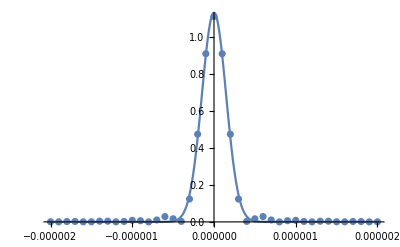

```mathematica
Show[{ListPlot[IPData1D, PlotRange-> All], Plot[fit1D[x], {x,-2μm,2μm}, PlotRange->  All]}]
```

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 4.81342 | 0.01367 | 352.116 | 5.1171×10^-128
waistFit | -3.67868×10^-7 | 2.8443×10^-9 | -129.335 | 1.00598×10^-93

0.00199278

```mathematica
4.55μm*(1+(z/zR)^2)^(1/2)/.{z-> 22mm, zR-> π*(4.55μm)^2/(461nm)}//N
```

0.000709531

```mathematica
.00071/(1.1mm)
```

0.645455

```mathematica
2/π//N
```

0.63662

```mathematica
1.3*5
```

6.5

```mathematica
magnification
```

6.75

```mathematica
(*These outputs agree with measured regal lab parameters to 10%, see my thesis or Brian's*)
```

```mathematica
speed =4.26*10^3;
EFL = 22mm;
waist = .0006;
magnification=27mm/(2*waist);
bandWidth = 30MHz;
wavelength = 852nm;
spacing = 1300nm;
```

## Analyzing rail system

#### 2D integral for the imaging system been testing 12/08

```mathematica
(37+39)*25.4
```

1930.4

```mathematica
19.5*25.4
```

495.3

```mathematica
13.5/1900
```

0.00710526

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,14.8mm,1930mm,(2π)/(515nm),.0071,10mm]]^2},{x,-40μm,40μm,4μm},{y,-40μm,40μm,4μm}],1];
```

```mathematica
13.5/1000
```

0.0135

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,14.16mm,1000mm,(2π)/(515nm),.0135,10mm]]^2},{x,-40μm,40μm,4μm},{y,-40μm,40μm,4μm}],1];
```

```mathematica
fit = NonlinearModelFit[IPData,A Exp[-2(x^2+y^2)/waistFit^2],{{A,1},{waistFit,35μm}},{x,y}];
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 1.46958×10^-7 | 4.35669×10^-10 | 337.315 | 2.67644122778×10^-532
waistFit | 0.0000172705 | 3.62038×10^-8 | 477.035 | 3.42316408554×10^-598

```mathematica
(*IPData = Flatten[Table[{x,y,photonDistribution[x,y]},{x,-1μm,1μm,0.1μm},{y,-1μm,1μm,0.15μm}],1];*)
```

```mathematica
1.7/30
```

0.0566667

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,1.7mm,30mm,(2π)/(515nm),0.056]]^2},{x,-10μm,10μm,0.1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
waistFit*(1+(z/(π*waistFit^2/(515nm)))^2)^(1/2)/.{z-> 30mm,fit1D["BestFitParameters"][[2]]}//N
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.00719281 | 0.0000181165 | 397.03 | 1.85206×10^-290
waistFit | 3.84942×10^-6 | 1.11954×10^-8 | 343.838 | 4.79724×10^-278

0.00127757

```mathematica
3.8*1740/220
```

30.0545

```mathematica
waistFit*(1+(z/(π*waistFit^2/(515nm)))^2)^(1/2)/.{z-> 30mm,waistFit-> 2.9μm}//N
```

0.00169583

```mathematica
Sin[ArcTan[13.5/1740]]
```

0.00775839

#### Determing size of beam after 18 EFL collimator, assuming 1.75 um fiber mode waist

```mathematica
3.5/2
```

1.75

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,1.70mm,18mm,(2π)/(515nm),0.25]]^2},{x,-50μm,50μm,1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0277862 | 5.90006×10^-6 | 4709.48 | 1.1549×10^-266
waistFit | 1.75037×10^-6 | 4.19254×10^-10 | 4174.96 | 1.74686×10^-261

#### Determing size of beam after 30 mm lens

```mathematica
(25.4/2)/30
```

0.423333

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,1.70mm,30mm,(2π)/(515nm),0.4]]^2},{x,-5μm,5μm,.1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0100588 | 5.98323×10^-7 | 16811.6 | 2.24763524249246×10^-321
waistFit | 2.90099×10^-6 | 1.99273×10^-10 | 14557.8 | 3.47004744642159×10^-315

#### Size of beam after 22 cm: 12.45 mm. Using time reversal to figure out waist at the lens given that going in reverse should give the spot from above.

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,12.45mm,220mm,(2π)/(515nm),0.2]]^2},{x,-50μm,50μm,1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.010032 | 5.98528×10^-7 | 16761.1 | 3.02732014474693×10^-321
waistFit | 2.90484×10^-6 | 2.0012×10^-10 | 14515.5 | 4.62917936614432×10^-315

#### Size of beam after long lens: using .0077 assuming iris sets NA

```mathematica
13.5/1740
```

0.00775862

```mathematica
IPData1D = Table[{x,Norm[IP1D[x,15.6mm,1740mm,(2π)/(515nm),0.0077]]^2},{x,-50μm,50μm,1μm}];
fit1D = NonlinearModelFit[IPData1D,A Exp[-2 x^2/waistFit^2],{A,{waistFit,1μm}},x];
fit1D["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.000154461 | 5.88256×10^-7 | 262.574 | 1.41422×10^-142
waistFit | 0.0000269583 | 1.18554×10^-7 | 227.392 | 2.11622×10^-136

#### Size of beam after long lens: using .0077 assuming iris sets NA

```mathematica
.0135*245/27
```

0.1225

```mathematica
IPData = Flatten[Table[{x,y,Norm[imagePlaneTheta[x,y,14.16mm,1000mm,(2π)/(515nm),.01225,10mm]]^2},{x,-40μm,40μm,4μm},{y,-40μm,40μm,4μm}],1];
```

```mathematica
fit = NonlinearModelFit[IPData,A Exp[-2(x^2+y^2)/waistFit^2],{{A,1},{waistFit,35μm}},{x,y}];
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 1.46958×10^-7 | 4.35669×10^-10 | 337.315 | 2.67644122778×10^-532
waistFit | 0.0000172705 | 3.62038×10^-8 | 477.035 | 3.42316408554×10^-598